# Time dependent speed and value differentiation

Time dependent speed demo

Field verbosity defaults to 1
Field arrayOrdering defaults to RowMajor
Field origin defaults to {0,0}
Field sndOrder defaults to 0
Field showProgress defaults to 0
Fast marching solver completed in 0.000269 s.
Field exportActiveNeighs defaults to 0
Field exportGeodesicFlow defaults to 0

Front first goes slow, then fast, then slow on the left side and fast on the right side

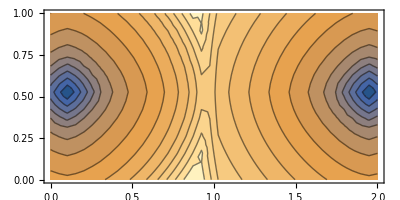

```mathematica
Module[{prms,n=20,dims,out,h},
dims={2n,n};
h=1/n;

prms={
(*Setup a very basic shortest path problem. The methods illustrated here apply to any model.*)
"dims"->dims,
"gridScale"->h,
"seeds"-> {{0.1,0.5},{1.9,0.5}},
"exportValues"->1,
"progressReportLandmarks"->{},

(*Time dependent speed. Speed is linearly interpolated between the provided times. 
(Falls back to first and last speed outside time bounds)*)
"speed_times"->{0.2,0.35,0.5},
"speed_0"->1, (*Slow propagation everywhere*)
"speed_1"->3, (*Fast propagation everywhere*)
"speed_2"->Array[If[#1≤n,1,3]&,dims] (*Slow left, fast right*)
};

out=RunExec["FileHFM_Isotropic2",prms];
Print["log"/.out];

Print["Front first goes slow, then fast, then slow on the left side and fast on the right side"];
Print[ListContourPlot[Transpose@("values"/.out),DataRange->{{0,2},{0,1}},AspectRatio->Automatic,Contours->15]];
];
```

Value differentiation demo

Field verbosity defaults to 1
Field arrayOrdering defaults to RowMajor
Field origin defaults to {0,0}
Field sndOrder defaults to 0
Field showProgress defaults to 0
Fast marching solver completed in 0.000201 s.
Field exportActiveNeighs defaults to 0
Field exportGeodesicFlow defaults to 0

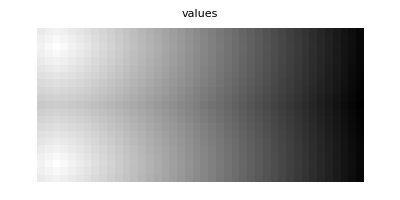

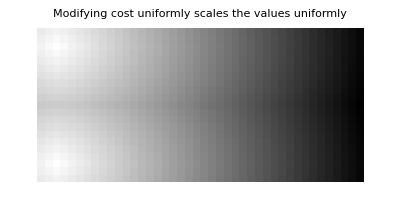

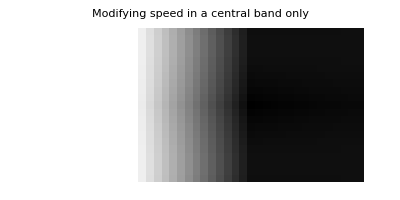

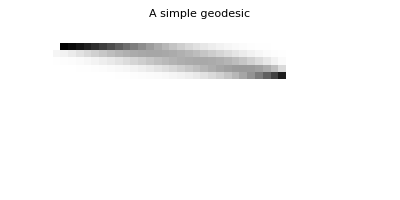

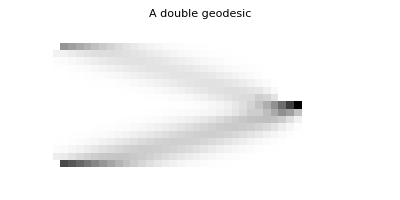

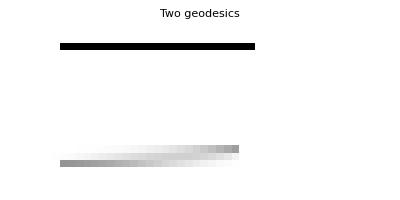

```mathematica
Module[{prms,n=21,dims,out,h,valueVariation},
dims={2n,n};
h=1/n;

prms={
(*Setup a very basic fast marching algorithm. The methods illustrated here apply to any model that inputs a "speed".*)
"dims"->dims,
"gridScale"->h,
"seeds"-> {{0.1,0.1},{0.1,0.9}},
"exportValues"->1,
"progressReportLandmarks"->{},
"speed"->1,

(*Forward differentation. Compute the first variation of the  values with respect to a variation in the speed function.*)
(*Here we test two two possible speed variations*)
"costVariation"->Array[
{1, (*First variation: increase speed uniformly*)
If[2n/3≤#1 && #1<=4n/3,1,0] (*Second variation, increase speed in a central band only*)
}&,dims],

(*Backward differentiation. Compute the sensitivity of the values a certain points w.r.t variations of the speed function.*)
"inspectSensitivity"->{{1.5,0.7},{1.6,0.5},{1.2,0.2},{1.3,0.9}},
(*optionally, group some points together*)
"inspectSensitivityLengths"->{1,1,2},
(*optionally, define weights for the different points*)
"inspectSensitivityWeights"->{1,1,0.3,0.7}
};
out=RunExec["FileHFM_Isotropic2",prms];  (*FileHFM_Isotropic also fits*)
Print["log"/.out];
Print[TablePlot["values"/.out,{PlotLabel->"values"}]];

valueVariation="valueVariation"/.out;
Print[TablePlot[valueVariation[[;;,;;,1]], {PlotLabel->"Modifying cost uniformly scales the values uniformly"}]];
Print[TablePlot[valueVariation[[;;,;;,2]], {PlotLabel->"Modifying speed in a central band only"}]];

Print[TablePlot["costSensitivity_0"/.out,{PlotLabel->"A simple geodesic"}]];
Print[TablePlot["costSensitivity_1"/.out,{PlotLabel->"A double geodesic"}]];
Print[TablePlot["costSensitivity_2"/.out,{PlotLabel->"Two geodesics"}]];
];
```